```mathematica
SetDirectory[NotebookDirectory[]];
beat=Import["data/beat_v12a.csv"][[2;;]];
myStyle[size_]:=Directive[FontFamily->"Times New Roman",size,Black];
```

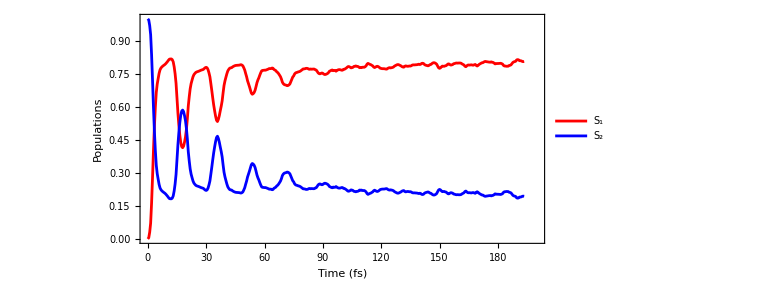

```mathematica
ListPlot[{
beat[[All,{1,3}]],
beat[[All,{1,4}]]
},
Joined->True,
Frame->True,
FrameStyle->myStyle[20],
FrameLabel->Table[Style[text,myStyle[20]],{text,{"Time (fs)","Populations"}}],
ImageSize->Large,
PlotRange->{{0,200},{0,1}},
AspectRatio->1/2,
PlotStyle->{Red,Blue},
PlotLegends->Placed[Table[Style[text,myStyle[20]],{text,{"S_1","S_2"}}],{0.9,0.62}]
]
```

```mathematica
BarLegend[{Blend[{Lighter[Lighter[Orange]],Lighter[Orange],Orange,Red,Black},#]&,{0,1}},4,LabelStyle->myStyle[20]]
```